{{1,17.3},{2,28.},{3,40.6},{4,53.1},{5,66.6},{6,80.3}}

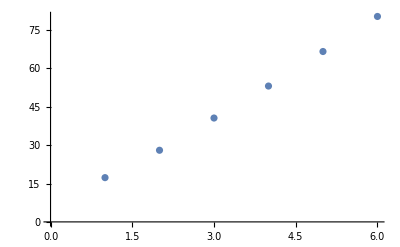

```mathematica
U1={17.3,28.0,40.6,53.1,66.6,80.3};
data1=Table[{i,U1[[i]]},{i,1,6}]
grp1=ListPlot[data1]
```

```mathematica
fd1=Fit[data1,{1,x},x]
```

3.32+12.6657 x

```mathematica
Needs["LinearRegression`"]
Regress[data1,{1,x},x,RegressionReport->{RSquared}]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

{RSquared→0.998428}

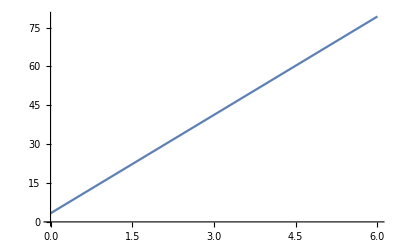

```mathematica
Plot[fd1,{x,0,6}]
```

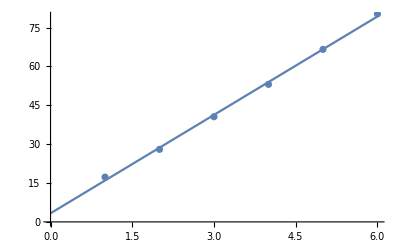

```mathematica
Show[%,grp1]
```

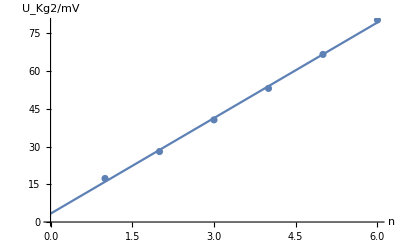

```mathematica
Show[%10,AxesLabel->{HoldForm[n],HoldForm[U_Kg2/mV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

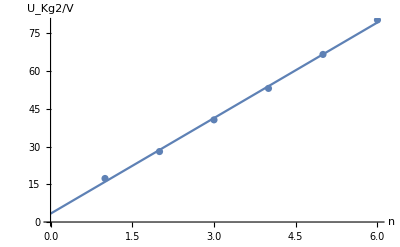

```mathematica
Show[%11,AxesLabel->{HoldForm[n],HoldForm[HoldForm[U_Kg2/V]]},PlotLabel->None]
```

{{1,4.},{2,8.7},{3,13.8},{4,18.5},{5,23.3},{6,28.4}}

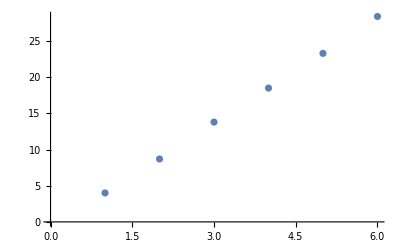

```mathematica
U2={4.0,8.7,13.8,18.5,23.3,28.4};
data2=Table[{i,U2[[i]]},{i,1,6}]
grp2=ListPlot[data2]
```

```mathematica
fd2=Fit[data2,{1,x},x]
```

-0.933333+4.87143 x

```mathematica
Regress[data2,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.999858}

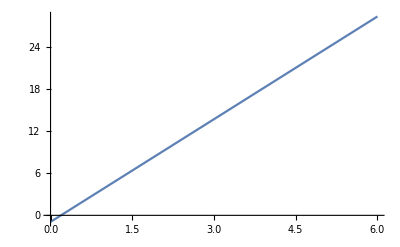

```mathematica
Plot[fd2,{x,0,6}]
```

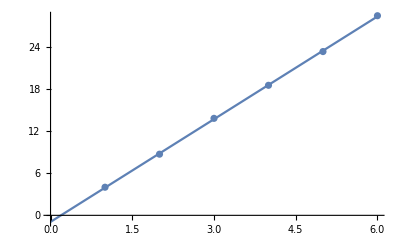

```mathematica
Show[%,grp2]
```

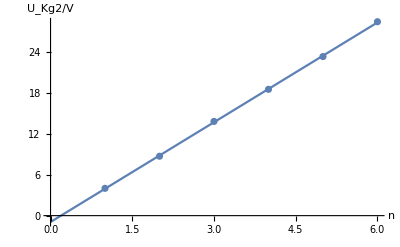

```mathematica
Show[%18,AxesLabel->{HoldForm[n],HoldForm[U_Kg2/V]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```